{{x→0},{x→-√μ},{x→√μ}}

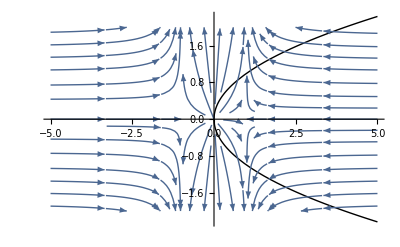

```mathematica
Clear[x,xdot,μ,y];
xdot=μ x-(x)^3;
Solve[xdot==0,x]
μ=1;
Plot[{μ x-x^2},{x,-1,1}];
Show[Plot[{Sqrt[μ],-Sqrt[μ]},{μ,-5,5},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{μ x-x^3,y},{x,-5,5},{y,-2,2},GridLines->Automatic,StreamScale->Medium]
]
```

For the non linear evolution equation that governs liquid film dynamics, the derivative of the growth rate equation resembles f(x,μ)=μ x - x^3.  For the liquid film, μ=(2 Pm/(1+Bi)^2 - 2 Pm)/Sn

```mathematica
μ=((2 Pm)/(Bi+1)^2-2 Pm)/Sn
```

{{x→0},{x→-√μ},{x→√μ}}

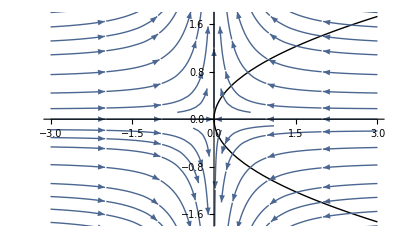

```mathematica
Clear[x,xdot,μ,y];
xdot=μ x-(x)^3;
Solve[xdot==0,x]
μ=-1;
μmax=3Abs[μ];
Plot[{μ x-x^2},{x,-1,1}];
Show[Plot[{Sqrt[μ],-Sqrt[μ]},{μ,-μmax,μmax},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{μ x-x^3,y},{x,-μmax,μmax},{y,-μmax,μmax},GridLines->Automatic,StreamScale->Medium]
]
```